```mathematica
outall2g=ToExpression[Import[NotebookDirectory[]<>"out-Er-dw-coupled-Ntraj.dat","TSV"]];
outall2g//Dimensions
```

{21,11,30,500,9}

```mathematica
dims=Dimensions[outall2g]
Gs=Range[0,2,0.2];Length[Gs]
ddw=Range[-1,1,0.1];Length[ddw]
```

{21,11,30,500,9}

11

21

```mathematica
rvsdw2zt={};
Gs=Range[0,2,0.2];
ddw=Range[-1,1,0.1];
Do[
rvsdw2x={};
ff [z_]:={ddw[[j]],z};
Do[out=outall2g[[j,i]];
AppendTo[rvsdw2x,ff /@ Sum[out[[itraj,it,5]],{it,1,dims[[4]]},{itraj,1,dims[[3]]}]]
,{i,1,Length[Gs]}];
AppendTo[rvsdw2zt,rvsdw2x];
,{j,1,Length[ddw]}];

rvsdw2zt//Dimensions
```

{21,11,10,2}

```mathematica
cols
```

{RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.2748608, 0.1822636, 0.7272788],RGBColor[0.2484884, 0.3863264, 0.813373],RGBColor[0.2979596, 0.5657928, 0.7522386000000001],RGBColor[0.38822480000000004, 0.674195, 0.6035436000000001],RGBColor[0.513417, 0.72992, 0.440682],RGBColor[0.6660832000000001, 0.7430418, 0.32293540000000004],RGBColor[0.8083416, 0.7110806, 0.255976],RGBColor[0.8935136, 0.6004149999999999, 0.2205464],RGBColor[0.8929546, 0.3896616, 0.1794008],RGBColor[0.857359, 0.131106, 0.132128]}

```mathematica
cols=Table[ColorData["Rainbow",t],{t,0,1,1/(Length[Gs]-1)}];
labels={"EhopsR","EhopsL","EinjR","EinjL","EextR","EextL","HinjR","HinjL","HextR","HextL"};
Manipulate[ListPlot[Table[rvsdw2zt[[;;,ie,ir,;;]],{ie,1,Length[Gs]}],Joined->True,PlotStyle->cols,PlotMarkers-> cols,PlotLabel->labels[[ir]],AxesLabel-> {"dw",""},PlotRange-> Full ],{ir,1,10,1}]
```

```mathematica
(* out: toRight, toLeft , total to right *)
iRates={{4,5,7,10},{3,6,8,9}};
dims=Dimensions[outall2g];
Gs=Range[0,2,0.2];
ddw=Range[-1,1,0.1];
rvsdw={};
Do[
rvsdw2x={};
ff [z_]:=({ddw[[j]],z});
Do[
XR=Sum[Sum[outall2g[[j,i,itraj,it,5,ii]],{itraj,1,dims[[3]]},{it,1,dims[[4]]}],{ii,{4,5,7,10}}];(* to right*)
XL=Sum[Sum[outall2g[[j,i,itraj,it,5,ii]],{itraj,1,dims[[3]]},{it,1,dims[[4]]}],{ii,{3,6,8,9}}];(* to left*)
X={ff/@{XR},ff/@{XL},ff/@{XR-XL}};
AppendTo[rvsdw2x,X];
,{i,1,Length[Gs]}];
AppendTo[rvsdw,rvsdw2x];
,{j,1,Length[ddw]}];
XR=rvsdw[[;;,;;,1,1,;;]]//Transpose;
XL=rvsdw[[;;,;;,2,1,;;]]//Transpose;
XtR=rvsdw[[;;,;;,3,1,;;]]//Transpose;
```

```mathematica
cols
```

{RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.2748608, 0.1822636, 0.7272788],RGBColor[0.2484884, 0.3863264, 0.813373],RGBColor[0.2979596, 0.5657928, 0.7522386000000001],RGBColor[0.38822480000000004, 0.674195, 0.6035436000000001],RGBColor[0.513417, 0.72992, 0.440682],RGBColor[0.6660832000000001, 0.7430418, 0.32293540000000004],RGBColor[0.8083416, 0.7110806, 0.255976],RGBColor[0.8935136, 0.6004149999999999, 0.2205464],RGBColor[0.8929546, 0.3896616, 0.1794008],RGBColor[0.857359, 0.131106, 0.132128]}

{RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.2748608, 0.1822636, 0.7272788],RGBColor[0.2484884, 0.3863264, 0.813373],RGBColor[0.2979596, 0.5657928, 0.7522386000000001],RGBColor[0.38822480000000004, 0.674195, 0.6035436000000001],RGBColor[0.513417, 0.72992, 0.440682],RGBColor[0.6660832000000001, 0.7430418, 0.32293540000000004],RGBColor[0.8083416, 0.7110806, 0.255976],RGBColor[0.8935136, 0.6004149999999999, 0.2205464],RGBColor[0.8929546, 0.3896616, 0.1794008],RGBColor[0.857359, 0.131106, 0.132128]}

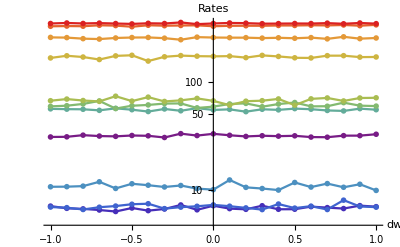

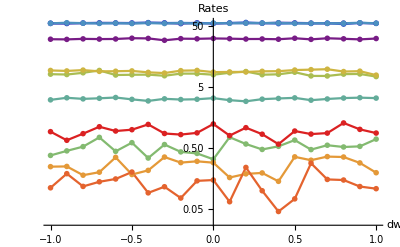

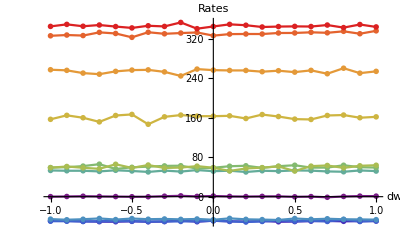

```mathematica
Gs=Range[0,2,0.2];
ddw=Range[-1,1,0.1];
XR=rvsdw[[;;,;;,1,1,;;]]//Transpose;
XL=rvsdw[[;;,;;,2,1,;;]]//Transpose;
XtR=rvsdw[[;;,;;,3,1,;;]]//Transpose;
cols=Table[ColorData["Rainbow",t],{t,0,1,1/(Length[Gs]-1)}]
labels={"EhopsR","EhopsL","EinjR","EinjL","EextR","EextL","HinjR","HinjL","HextR","HextL"};
ListLogPlot[XR,Joined->True,PlotStyle->cols,PlotMarkers-> cols,AxesLabel-> {"dw","Rates"} ]
ListLogPlot[XL,Joined->True,PlotStyle->cols,PlotMarkers-> cols,AxesLabel-> {"dw","Rates"} ]
ListPlot[XtR,Joined->True,PlotStyle->cols,PlotMarkers-> cols,AxesLabel-> {"dw","Rates"} ]
```

{RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.3431304, 0.11581720000000001, 0.6369784000000001],RGBColor[0.2748608, 0.1822636, 0.7272788],RGBColor[0.2480688, 0.2797284, 0.7879248],RGBColor[0.2484884, 0.3863264, 0.813373],RGBColor[0.266122, 0.486664, 0.802529],RGBColor[0.2979596, 0.5657928, 0.7522386000000001],RGBColor[0.3386556, 0.6276854, 0.6832816],RGBColor[0.38822480000000004, 0.674195, 0.6035436000000001],RGBColor[0.446557, 0.7074632, 0.5203932],RGBColor[0.513417, 0.72992, 0.440682],RGBColor[0.5888042, 0.7409584, 0.37500680000000003],RGBColor[0.6660832000000001, 0.7430418, 0.32293540000000004],RGBColor[0.7408424, 0.7340177999999999, 0.2838318],RGBColor[0.8083416, 0.7110806, 0.255976],RGBColor[0.863512, 0.670771, 0.236564],RGBColor[0.8935136, 0.6004149999999999, 0.2205464],RGBColor[0.9021174, 0.5055088, 0.2018252],RGBColor[0.8929546, 0.3896616, 0.1794008],RGBColor[0.8739574, 0.2607876, 0.15481040000000001],RGBColor[0.857359, 0.131106, 0.132128]}

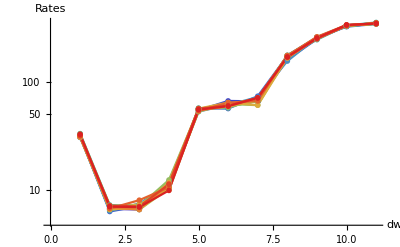

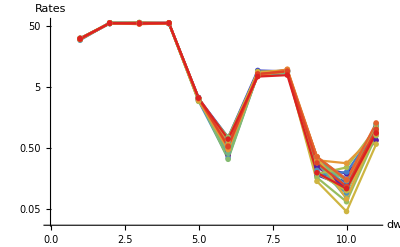

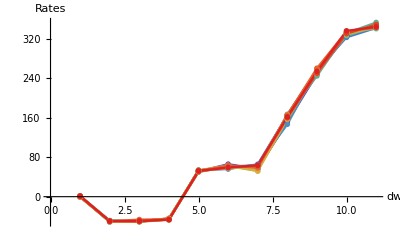

```mathematica
XR=rvsdw[[;;,;;,1,1,2]];
XL=rvsdw[[;;,;;,2,1,2]];
XtR=rvsdw[[;;,;;,3,1,2]];
cols=Table[ColorData["Rainbow",t],{t,0,1,1/(Length[ddw]-1)}]
labels={"EhopsR","EhopsL","EinjR","EinjL","EextR","EextL","HinjR","HinjL","HextR","HextL"};
ListLogPlot[XR,Joined->True,PlotStyle->cols,PlotMarkers-> cols,AxesLabel-> {"dw","Rates"} ]
ListLogPlot[XL,Joined->True,PlotStyle->cols,PlotMarkers-> cols,AxesLabel-> {"dw","Rates"} ]
ListPlot[XtR,Joined->True,PlotStyle->cols,PlotMarkers-> cols,AxesLabel-> {"dw","Rates"} ]
```

{21,11,1,2}

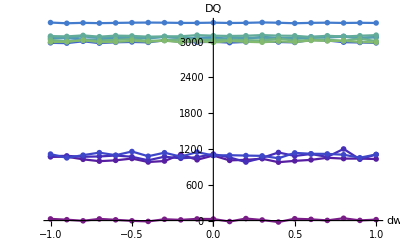

```mathematica
(* out: toRight, toLeft , total to right *)
iRates={{4,5,7,10},{3,6,8,9}};
dims=Dimensions[outall2g];
Gs=Range[0,2,0.2];
ddw=Range[-1,1,0.1];

rvsdw2={};
Do[
rvsdw2x={};
ff [z_]:=({ddw[[j]],z});
Do[
XR=Sum[outall2g[[j,i,itraj,it,3]],{itraj,1,dims[[3]]},{it,1,dims[[4]]}];
AppendTo[rvsdw2x,ff/@{XR}];
,{i,1,Length[Gs]}];
AppendTo[rvsdw2,rvsdw2x];
,{j,1,Length[ddw]}];

Dimensions[rvsdw2]
ListPlot[Table[rvsdw2[[;;,ie,1,;;]],{ie,1,Length[Gs]}],Joined->True,PlotStyle->cols,PlotMarkers-> cols,AxesLabel-> {"dw","DQ"} ]
```

```mathematica
Dimensions[rvsdw2]
```

{}

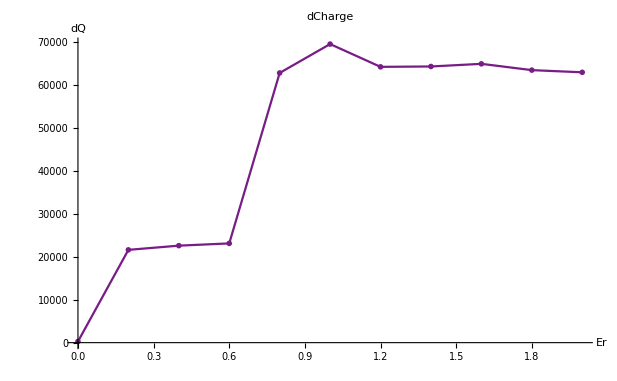

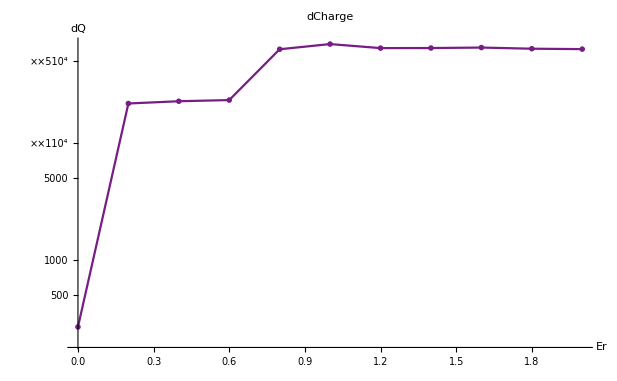

```mathematica
sum=Sum[rvsdw2[[i,;;,1,2]],{i,1,Length[ddw]}];
ListPlot[Table[{Gs[[i]],sum[[i]]},{i,1,Length[Gs]}],Joined->True,PlotStyle->cols[[1]],PlotMarkers->cols[[1]],PlotLabel-> "dCharge",AxesLabel-> {"Er","dQ"} ]
ListLogPlot[Table[{Gs[[i]],sum[[i]]},{i,1,Length[Gs]}],Joined->True,PlotStyle->cols[[1]],PlotMarkers->cols[[1]],PlotLabel-> "dCharge",AxesLabel-> {"Er","dQ"} ]
```

```mathematica
(* out: toRight, toLeft , total to right *)
iRates={{4,5,7,10},{3,6,8,9}};
dims=Dimensions[outall2g];
Gs=Range[0,2,0.2];
ddw=Range[-1,1,0.1];


rvsdw2zt={};
Do[
rvsdw2x={};
ff [z_]:=({ddw[[j]],z});
Do[
XR=Sum[outall2g[[j,i,itraj,it,4]],{itraj,1,dims[[3]]},{it,1,dims[[4]]}];
AppendTo[rvsdw2x,ff/@{XR}];
,{i,1,Length[Gs]}];
AppendTo[rvsdw2zt,rvsdw2x];
,{j,1,Length[ddw]}];
```

```mathematica
Dimensions[rvsdw2]
```

{21,11,1,2}

```mathematica
Gs=Range[0,2,0.2]
```

{0.,0.2,0.4,0.6,0.8,1.,1.2,1.4,1.6,1.8,2.}

11

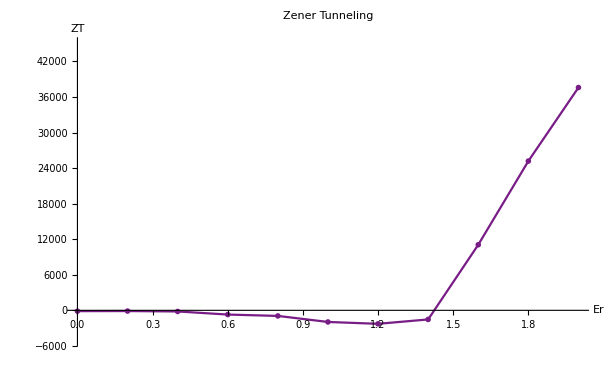

```mathematica
sum=Sum[rvsdw2zt[[i,;;,1,2]],{i,1,Length[ddw]}];
ListPlot[Table[{Gs[[i]],sum[[i]]},{i,1,Length[Gs]}],Joined->True,PlotStyle->cols[[1]],PlotMarkers->cols[[1]],PlotLabel-> "Zener Tunneling",AxesLabel-> {"Er","ZT"} ,PlotRange-> {-5000,45000}]
```

```mathematica
outall2g2=ToExpression[Import[NotebookDirectory[]<>"out-Er-dw-uncoupled-Ntraj.dat","TSV"]];
dims2=Dimensions[outall2g2]

Gs2=Range[0,2,0.1];Length[Gs2]
ddw2=Range[0,1,1];Length[ddw2]
```

{2,21,1,300,9}

21

2

```mathematica
(* out: toRight, toLeft , total to right *)
iRates={{4,5,7,10},{3,6,8,9}};

rvsdw22={};
Do[
rvsdw2x={};
ff [z_]:=({ddw2[[j]],z});
Do[
XR=Sum[outall2g2[[j,i,1,it,3]],{it,1,dims2[[4]]}];
AppendTo[rvsdw2x,ff/@{XR}];
,{i,1,Length[Gs2]}];
AppendTo[rvsdw22,rvsdw2x];
,{j,1,Length[ddw2]}];

cols2=Table[ColorData["Rainbow",t],{t,0,1,1/(Length[ddw2]-1)}]

Dimensions[rvsdw22]
```

{RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.857359, 0.131106, 0.132128]}

{2,21,1,2}

```mathematica
cols=Table[ColorData["Rainbow",t],{t,0,1,1/(Length[ddw]-1)}]
```

{RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.3431304, 0.11581720000000001, 0.6369784000000001],RGBColor[0.2748608, 0.1822636, 0.7272788],RGBColor[0.2480688, 0.2797284, 0.7879248],RGBColor[0.2484884, 0.3863264, 0.813373],RGBColor[0.266122, 0.486664, 0.802529],RGBColor[0.2979596, 0.5657928, 0.7522386000000001],RGBColor[0.3386556, 0.6276854, 0.6832816],RGBColor[0.38822480000000004, 0.674195, 0.6035436000000001],RGBColor[0.446557, 0.7074632, 0.5203932],RGBColor[0.513417, 0.72992, 0.440682],RGBColor[0.5888042, 0.7409584, 0.37500680000000003],RGBColor[0.6660832000000001, 0.7430418, 0.32293540000000004],RGBColor[0.7408424, 0.7340177999999999, 0.2838318],RGBColor[0.8083416, 0.7110806, 0.255976],RGBColor[0.863512, 0.670771, 0.236564],RGBColor[0.8935136, 0.6004149999999999, 0.2205464],RGBColor[0.9021174, 0.5055088, 0.2018252],RGBColor[0.8929546, 0.3896616, 0.1794008],RGBColor[0.8739574, 0.2607876, 0.15481040000000001],RGBColor[0.857359, 0.131106, 0.132128]}

```mathematica
{21,11,30,500,9}
```

```mathematica
Dimensions[outall2g]
Dimensions[outall2g2]
```

{21,11,30,500,9}

{2,21,1,300,9}

```mathematica
norm=Product[Dimensions[outall2g][[i]],{i,{1,3,4}}]
norm2=Product[Dimensions[outall2g2][[i]],{i,{1,3,4}}]
```

315000

600

```mathematica
sum=Sum[rvsdw2[[i,;;,1,2]],{i,1,Length[ddw]}]/norm;
sum2=Sum[rvsdw22[[i,;;,1,2]],{i,1,Length[ddw2]}]/norm2;
```

```mathematica
pl=Table[{Gs[[i]],sum[[i]]},{i,1,Length[Gs]}];
pl2=Table[{Gs2[[i]],sum2[[i]]},{i,1,Length[Gs2]}];
```

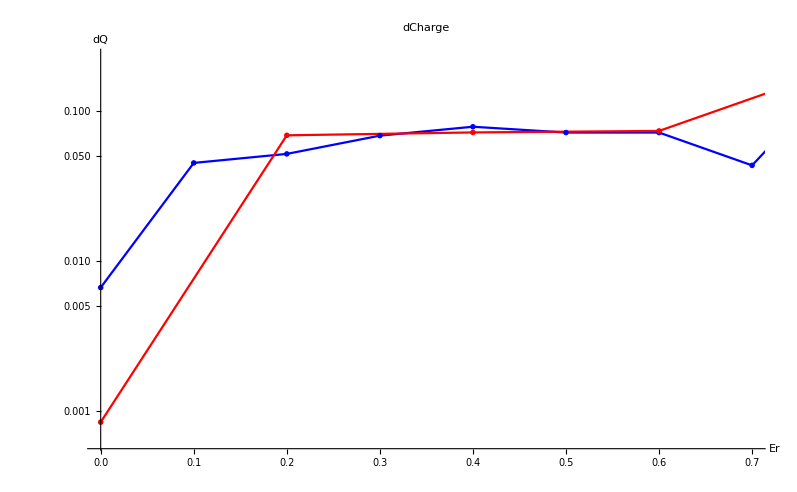

```mathematica
ListLogPlot[{pl2,pl},Joined->True,PlotStyle->{Blue,Red},PlotMarkers->{Blue,Red},PlotLabel-> "dCharge",AxesLabel-> {"Er","dQ"} ,PlotRange-> {{0,0.7},Automatic}]
```